```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\factorial_cumulant\chidata_freezeout

# Factorial Cumulants From fRG Data

## Relations between cumulants and Factorial Cumulants

## Single Variable case

Relations between Cumulants and Factorial Cumulants
⟨N^m⟩_fc=⟨N(N-1)…(N-m+1)⟩_c

So some values of m can be obtain:
m=1:
⟨N⟩_fc=⟨N⟩_c=C_1

m=2:
⟨N^2⟩_fc=⟨N^2⟩_c-⟨N⟩_c=C_2-C_1

m=3:
⟨N^3⟩_fc=⟨N(N-1)(N-2)⟩_c

```mathematica
Expand[Nb(Nb-1)(Nb-2)]
```

2 Nb-3 Nb^2+Nb^3

⟨N^3⟩_fc=⟨N^3⟩_c-3⟨N^2⟩_c+2⟨N⟩_c=C_3-3 C_2+2 C_1

m=4:
⟨N^4⟩_fc=⟨N(N-1)(N-2)(N-3)⟩_c

```mathematica
Expand[Nb(Nb-1)(Nb-2)(Nb-3)]
```

-6 Nb+11 Nb^2-6 Nb^3+Nb^4

⟨N^4⟩_fc=⟨N^4⟩_c-6⟨N^3⟩_c+11⟨N^2⟩_c-6⟨N⟩_c=C_4-6 C_3+11 C_2-6 C_1

m=5:
⟨N^5⟩_fc=⟨N(N-1)(N-2)(N-3)(N-4)⟩_c

```mathematica
Expand[Nb(Nb-1)(Nb-2)(Nb-3)(Nb-4)]
```

24 Nb-50 Nb^2+35 Nb^3-10 Nb^4+Nb^5

⟨N^5⟩_fc=⟨N^5⟩_c-10⟨N^4⟩_c+35⟨N^3⟩_c-50⟨N^2⟩_c+24⟨N⟩_c=C_5-10 C_4+35 C_3-50 C_2+24 C_1

m=6:
⟨N^6⟩_fc=⟨N(N-1)(N-2)(N-3)(N-4)(N-5)⟩_c

```mathematica
Expand[Nb(Nb-1)(Nb-2)(Nb-3)(Nb-4)(Nb-5)]
```

-120 Nb+274 Nb^2-225 Nb^3+85 Nb^4-15 Nb^5+Nb^6

⟨N^6⟩_fc=⟨N^6⟩_c-15⟨N^5⟩_c+85⟨N^4⟩_c-225⟨N^3⟩_c+274⟨N^2⟩_c-120⟨N⟩_c=C_6-15 C_5+85 C_4-225 C_3+274 C_2-120 C_1

## Two Variable case

### C1net

Relations between Cumulants and Factorial Cumulants
⟨N_B^m_1(N_(B̄))^m_2⟩_fc=⟨N_B(N_B-1)…(N_B-m_1+1)
                   N_(B̄)(N_(B̄)-1)…(N_(B̄)-m_2+1)⟩_c
N_net=N_B-N_(B̄)  Net Baryon number
N_tot=N_B+N_(B̄)  Total Baryon number

So some values of m can be obtain:
C_1^fc:
⟨N_net⟩_fc=⟨N_B-N_(B̄)⟩_fc=⟨N_B⟩_fc-⟨N_(B̄)⟩_fc=⟨N_B⟩_c-⟨N_(B̄)⟩_c=⟨N_net⟩_c=C_1^net

### C2net

C_2^fc:
⟨N_net^2⟩_fc=⟨(N_B-N_(B̄))^2⟩_fc
                    =⟨N_B^2+(N_(B̄))^2-2 N_B N_(B̄)⟩_fc
                    =⟨N_B^2⟩_fc+⟨(N_(B̄))^2⟩_fc-2⟨N_B N_(B̄)⟩_fc
                    =⟨N_B(N_B-1)⟩_c+⟨N_(B̄)(N_(B̄)-1)⟩_c-2⟨N_B N_(B̄)⟩_c
                    =⟨N_B^2-N_B+(N_(B̄))^2-N_(B̄)-2 N_B N_(B̄)⟩_c
                    =⟨(N_B-N_(B̄))^2-(N_B+N_(B̄))⟩_c
                    =⟨N_net^2⟩_c-⟨N_tot⟩_c
                    =C_2^net-C_1^tot

### C3net

C_3^fc:
⟨N_net^3⟩_fc=⟨(N_B-N_(B̄))^3⟩_fc
                    =⟨N_B^3-(N_(B̄))^3-3 N_B^2 N_(B̄)+3 N_B(N_(B̄))^2⟩_fc
                    =⟨N_B(N_B-1)(N_B-2)⟩_c-⟨N_(B̄)(N_(B̄)-1)(N_(B̄)-2)⟩_c-3⟨N_B(N_B-1)N_(B̄)⟩_c+3⟨N_B N_(B̄)(N_(B̄)-1)⟩_c
                    =⟨N_B^3-3 N_B^2+2 N_B-(N_(B̄))^3+3(N_(B̄))^2-2 N_(B̄)+3(-N_B^2 N_(B̄)+N_B N_(B̄)+N_B(N_(B̄))^2-N_B N_(B̄))⟩_c
                    =⟨(N_B-N_(B̄))^3-3(N_B+N_(B̄))(N_B-N_(B̄))+2(N_B-N_(B̄))⟩_c
                    =⟨N_net^3⟩_c-3⟨N_net N_tot⟩_c+2⟨N_net⟩_c
                    =C_3^net-3(C_(1,1))^(net,tot)+2 C_1^net

### C4net

C_4^fc:
⟨N_net^4⟩_fc=⟨(N_B-N_(B̄))^4⟩_fc
                    =⟨N_B^4+(N_(B̄))^4+6 N_B^2(N_(B̄))^2-4 N_B^3 N_(B̄)-4 N_B(N_(B̄))^3⟩_fc
                    =⟨N_B^4⟩_fc+⟨(N_(B̄))^4⟩_fc+6⟨N_B^2(N_(B̄))^2⟩_fc-4⟨N_B^3 N_(B̄)⟩_fc-4⟨N_B(N_(B̄))^3⟩_fc

```mathematica
Expand[Nb(Nb-1)(Nb-2)(Nb-3)]
```

-6 Nb+11 Nb^2-6 Nb^3+Nb^4

```mathematica
Expand[Nbb(Nbb-1)(Nbb-2)(Nbb-3)]
```

-6 Nbb+11 Nbb^2-6 Nbb^3+Nbb^4

```mathematica
Expand[Nb(Nb-1)Nbb(Nbb-1)]
```

Nb Nbb-Nb^2 Nbb-Nb Nbb^2+Nb^2 Nbb^2

```mathematica
Expand[Nb(Nb-1)(Nb-2)Nbb]
```

2 Nb Nbb-3 Nb^2 Nbb+Nb^3 Nbb

```mathematica
Expand[Nb Nbb(Nbb-1)(Nbb-2)]
```

2 Nb Nbb-3 Nb Nbb^2+Nb Nbb^3

=⟨N_B^4⟩_c-6⟨N_B^3⟩_c+11⟨N_B^2⟩_c-6⟨N_B⟩_c
+⟨(N_(B̄))^4⟩_c-6⟨(N_(B̄))^3⟩_c+11⟨(N_(B̄))^2⟩_c-6⟨N_(B̄)⟩_c
+6⟨N_B^2(N_(B̄))^2-N_B^2 N_(B̄)-N_B(N_(B̄))^2+N_B N_(B̄)⟩_c
-4⟨N_B^3 N_(B̄)-3 N_B^2 N_(B̄)+2 N_B N_(B̄)⟩_c
-4⟨N_B(N_(B̄))^3-3 N_B(N_(B̄))^2+2 N_B N_(B̄)⟩_c
We have
N_net=N_B-N_(B̄)
N_tot=N_B+N_(B̄)
Then we can obtain
N_B=(N_net+N_tot)/2
N_(B̄)=(N_tot-N_net)/2

```mathematica
Expand[(-6 Nb+11 Nb^2-6 Nb^3+Nb^4)+(-6 Nbb+11 Nbb^2-6 Nbb^3+Nbb^4)+6(Nb Nbb-Nb^2 Nbb-Nb Nbb^2+Nb^2 Nbb^2)-4(2 Nb Nbb-3 Nb^2 Nbb+Nb^3 Nbb)-4(2 Nb Nbb-3 Nb Nbb^2+Nb Nbb^3)/.{Nb->(Nnet+Ntot)/2,Nbb->(Ntot-Nnet)/2}//Simplify]
```

8 Nnet^2+Nnet^4-6 Ntot-6 Nnet^2 Ntot+3 Ntot^2

Then we have
⟨N_net^4⟩_fc=⟨N_net^4⟩_c-6⟨N_net^2 N_tot⟩_c+3⟨N_tot^2⟩_c+8⟨N_net^2⟩_c-6⟨N_tot⟩_c
                    =C_4^net-6(C_(2,1))^(net,tot)+3 C_2^tot+8 C_2^net-6 C_1^tot

### C5net

C_5^fc:
⟨N_net^5⟩_fc=⟨(N_B-N_(B̄))^5⟩_fc
                    =⟨N_B^5-(N_(B̄))^5-5 N_B^4 N_(B̄)+5 N_B(N_(B̄))^4+10 N_B^3(N_(B̄))^2-10 N_B^2(N_(B̄))^3⟩_fc

```mathematica
Expand[(Nb-Nbb)^5]
```

Nb^5-5 Nb^4 Nbb+10 Nb^3 Nbb^2-10 Nb^2 Nbb^3+5 Nb Nbb^4-Nbb^5

```mathematica
Nb5=Expand[Nb(Nb-1)(Nb-2)(Nb-3)(Nb-4)];(*Subscript[N, B]^5*)
Nbb5=Expand[Nbb(Nbb-1)(Nbb-2)(Nbb-3)(Nbb-4)];(*Subscript[N, B̄]^5*)
Nb4Nbb1=-5Expand[Nb(Nb-1)(Nb-2)(Nb-3)Nbb];(*Subscript[N, B]^4 Subscript[N, B̄]*)
Nb1Nbb4=5Expand[Nb Nbb(Nbb-1)(Nbb-2)(Nbb-3)];(*Subscript[N, B] Subscript[N, B̄]^4*)
Nb3Nbb2=10Expand[Nb(Nb-1)(Nb-2) Nbb(Nbb-1)];(*Subscript[N, B]^3 Subscript[N, B̄]^2*)
Nb2Nbb3=-10Expand[Nb(Nb-1) Nbb(Nbb-1)(Nbb-2)];(*Subscript[N, B]^2 Subscript[N, B̄]^3*)
```

```mathematica
Collect[Expand[Nb5+Nbb5+Nb4Nbb1+Nb1Nbb4+Nb3Nbb2+Nb2Nbb3/.{Nb->(Nnet+Ntot)/2,Nbb->(Ntot-Nnet)/2}(*/.{Ntot->Nnet}*)//FullSimplify],{Nnet^5,Ntot^5,Nnet^4 Ntot,Nnet Ntot^4,Nnet^3 Ntot^2,Nnet^2 Ntot^3,Nnet^4,Ntot^4,Nnet^3 Ntot,Nnet Ntot^3,Nnet^2 Ntot^2,Nnet^2 Ntot,Nnet Ntot^2,Nnet^3,Ntot^3,Nnet^2,Ntot^2,Nnet Ntot,Nnet Ntot,Nnet,Ntot}]
```

-25 Nnet^2+(45 Nnet^3)/4-(5 Nnet^4)/4+(15 Nnet^5)/16+24 Ntot+(105 Nnet^2 Ntot)/4-5 Nnet^3 Ntot+(5 Nnet^4 Ntot)/16-25 Ntot^2-(45 Nnet Ntot^2)/4-(15 Nnet^2 Ntot^2)/2-(5 Nnet^3 Ntot^2)/8+(35 Ntot^3)/4+5 Nnet Ntot^3+(5 Nnet^2 Ntot^3)/8-(5 Ntot^4)/4-(5 Nnet Ntot^4)/16+Ntot^5/16

Then we have
⟨N_net^5⟩_fc=(⟨N_tot^5⟩_c+15⟨N_net^5⟩_c-5⟨N_net N_tot^4⟩_c+5⟨N_net^4 N_tot⟩_c-10⟨N_net^3 N_tot^2⟩_c+10⟨N_net^2 N_tot^3⟩_c)/16+(-5⟨N_net^4⟩_c-20⟨N_net^3 N_tot⟩_c-30⟨N_net^2 N_tot^2⟩_c+20⟨N_net N_tot^3⟩_c-5⟨N_tot^4⟩_c)/4+(45⟨N_net^3⟩_c+105⟨N_net^2 N_tot⟩_c-45⟨N_net N_tot^2⟩_c+35⟨N_tot^3⟩_c)/4+(-25⟨N_net^2⟩_c-25⟨N_tot^2⟩_c)+24⟨N_tot⟩_c
=1/16(C_5^tot+15 C_5^net-5(C_(1,4))^(net,tot)+5(C_(4,1))^(net,tot)-10(C_(3,2))^(net,tot)+10(C_(2,3))^(net,tot))+1/4(-5 C_4^net-20(C_(3,1))^(net,tot)-30(C_(2,2))^(net,tot)+20(C_(1,3))^(net,tot)-5 C_4^tot)+1/4(45 C_3^net+105(C_(2,1))^(net,tot)-45(C_(1,2))^(net,tot)+35 C_3^tot)+(-25 C_2^net-25 C_2^tot)+24 C_1^tot

### C6net

C_6^fc:
⟨N_net^6⟩_fc=⟨(N_B-N_(B̄))^6⟩_fc
                    =⟨N_B^6-6 N_B^5 N_(B̄)+15 N_B^4(N_(B̄))^2-20 N_B^3(N_(B̄))^3+15 N_B^2(N_(B̄))^4-6 N_B(N_(B̄))^5+(N_(B̄))^6⟩_fc

```mathematica
Expand[(Nb-Nbb)^6]
```

Nb^6-6 Nb^5 Nbb+15 Nb^4 Nbb^2-20 Nb^3 Nbb^3+15 Nb^2 Nbb^4-6 Nb Nbb^5+Nbb^6

```mathematica
Nb6=Expand[Nb(Nb-1)(Nb-2)(Nb-3)(Nb-4)(Nb-5)];(*Subscript[N, B]^6*)
Nbb6=Expand[Nbb(Nbb-1)(Nbb-2)(Nbb-3)(Nbb-4)(Nbb-5)];(*Subscript[N, B̄]^6*)
Nb5Nbb1=-6Expand[Nb(Nb-1)(Nb-2)(Nb-3)(Nb-4)Nbb];(*Subscript[N, B]^5 Subscript[N, B̄]*)
Nb1Nbb5=-6Expand[Nb Nbb(Nbb-1)(Nbb-2)(Nbb-3)(Nbb-4)];(*Subscript[N, B] Subscript[N, B̄]^5*)
Nb4Nbb2=15Expand[Nb(Nb-1)(Nb-2)(Nb-3) Nbb(Nbb-1)];(*Subscript[N, B]^4 Subscript[N, B̄]^2*)
Nb2Nbb4=15Expand[Nb(Nb-1) Nbb(Nbb-1)(Nbb-2)(Nbb-3)];(*Subscript[N, B]^2 Subscript[N, B̄]^4*)
Nb3Nbb3=-20Expand[Nb(Nb-1)(Nb-2) Nbb(Nbb-1)(Nbb-2)];(*Subscript[N, B]^3 Subscript[N, B̄]^3*)
```

```mathematica
(*Collect[*)Expand[Nb6+Nbb6+Nb5Nbb1+Nb1Nbb5+Nb4Nbb2+Nb2Nbb4+Nb3Nbb3/.{Nb->(Nnet+Ntot)/2,Nbb->(Ntot-Nnet)/2}(*/.{Ntot->Nnet}*)//FullSimplify](*,{Nnet^5,Ntot^5,Nnet^4 Ntot,Nnet Ntot^4,Nnet^3 Ntot^2,Nnet^2 Ntot^3,Nnet^4,Ntot^4,Nnet^3 Ntot,Nnet Ntot^3,Nnet^2 Ntot^2,Nnet^2 Ntot,Nnet Ntot^2,Nnet^3,Ntot^3,Nnet^2,Ntot^2,Nnet Ntot,Nnet Ntot,Nnet,Ntot}]*)
```

184 Nnet^2+40 Nnet^4+Nnet^6-120 Ntot-210 Nnet^2 Ntot-15 Nnet^4 Ntot+90 Ntot^2+45 Nnet^2 Ntot^2-15 Ntot^3

Then we have
⟨N_net^6⟩_fc=⟨N_net^6⟩_c-15⟨N_net^4 N_tot⟩_c+40⟨N_net^4⟩_c+45⟨N_net^2 N_tot^2⟩_c-210⟨N_net^2 N_tot⟩_c-15⟨N_tot^3⟩_c+184⟨N_net^2⟩_c+90⟨N_tot^2⟩_c-120⟨N_tot⟩_c
=C_6^net-15(C_(4,1))^(net,tot)+40 C_4^net+45(C_(2,2))^(net,tot)-210(C_(2,1))^(net,tot)-15 C_3^tot+184 C_2^net+90 C_2^tot-120 C_1^tot

## Data Import and compute

## Import data

### fRG data

```mathematica
sqrtsfrg=Flatten[Import["./STARFitI/sqrts.dat"]];
chi1STARII=Flatten[Import["./STARFitII/chi1.dat"]];
chi2STARII=Flatten[Import["./STARFitII/chi2.dat"]];
chi3STARII=Flatten[Import["./STARFitII/chi3.dat"]];
chi4STARII=Flatten[Import["./STARFitII/chi4.dat"]];
chi5STARII=Flatten[Import["./STARFitII/chi5.dat"]];
chi6STARII=Flatten[Import["./STARFitII/chi6.dat"]];
chi1STARI=Flatten[Import["./STARFitI/chi1.dat"]];
chi2STARI=Flatten[Import["./STARFitI/chi2.dat"]];
chi3STARI=Flatten[Import["./STARFitI/chi3.dat"]];
chi4STARI=Flatten[Import["./STARFitI/chi4.dat"]];
chi5STARI=Flatten[Import["./STARFitI/chi5.dat"]];
chi6STARI=Flatten[Import["./STARFitI/chi6.dat"]];
chi1An=Flatten[Import["./Andronic/chi1.dat"]];
chi2An=Flatten[Import["./Andronic/chi2.dat"]];
chi3An=Flatten[Import["./Andronic/chi3.dat"]];
chi4An=Flatten[Import["./Andronic/chi4.dat"]];
chi5An=Flatten[Import["./Andronic/chi5.dat"]];
chi6An=Flatten[Import["./Andronic/chi6.dat"]];
sqrtsfRG=Flatten[Import["./STARFitII/sqrts.dat"]];
```

```mathematica
ListLinePlot[Transpose[{sqrts,chi4STARII/chi2STARII}],ScalingFunctions->{"Log",Automatic}]
```

Transpose::nmtx: {sqrts,{0.66431,0.663818,0.662866,0.661214,0.659101,0.655831,0.6464,0.637874,0.631552,0.626498,0.618994,0.597245,0.579581,0.57704,0.57435,0.571461,0.568261,0.564798,0.561149,0.557396,0.551798,«10»,0.443188,0.428478,0.415085,0.403051,0.392441,0.383544,0.376986,0.37218,0.36914,0.363647,0.343691,0.325325,0.308553,0.294334,0.283792,0.276111,0.272212,0.274292,0.280375,«110»}} 的前两层无法转置.

ListLinePlot::lpn: {sqrts,{0.66431,0.663818,0.662866,0.661214,0.659101,0.655831,0.6464,0.637874,0.631552,0.626498,«31»,0.343691,0.325325,0.308553,0.294334,0.283792,0.276111,0.272212,0.274292,0.280375,«110»}}^T 不是由数字或者数对组成的列表.

ListLinePlot[Transpose[{sqrts,{0.66431,0.663818,0.662866,0.661214,0.659101,0.655831,0.6464,0.637874,0.631552,0.626498,0.618994,0.597245,0.579581,0.57704,0.57435,0.571461,0.568261,0.564798,0.561149,0.557396,0.551798,0.53924,0.527071,0.515372,0.504211,0.495237,0.486938,0.479378,0.472589,0.466605,0.459121,0.443188,0.428478,0.415085,0.403051,0.392441,0.383544,0.376986,0.37218,0.36914,0.363647,0.343691,0.325325,0.308553,0.294334,0.283792,0.276111,0.272212,0.274292,0.280375,0.283359,0.257266,0.231706,0.211671,0.19641,0.187773,0.190806,0.202172,0.228765,0.265957,0.304938,0.295162,0.302107,0.327303,0.376244,0.429154,0.42752,0.454307,0.520291,0.622128,0.743836,0.826654,0.939876,1.05439,1.21195,1.3618,1.5317,1.72531,1.93922,2.15516,2.43181,2.6993,2.98634,3.26111,3.57896,3.91351,4.26428,4.62379,4.98607,5.3432,5.69578,6.06217,6.32854,6.6236,6.89395,7.13661,7.33437,7.50844,7.64466,7.72182,7.80688,7.84578,7.84671,7.83008,7.76691,7.68108,7.5543,7.41712,7.26348,7.12721,6.98334,6.80804,6.60502,6.4122,6.26108,6.07257,5.89807,5.71565,5.60775,5.51366,5.26769,5.15853,4.95747,4.85975,4.65675,4.56061,4.38913,4.29171,4.11753,4.04571,3.88365,3.81424,3.66306,3.61898,3.44067,3.41511,3.28439,3.23503,3.1131,3.08635,2.99408,2.91674,2.85765,2.80192,2.72621,2.68273,2.61629,2.59193,2.51555,2.49436,2.40953,2.40836,2.33,2.31742,2.25529,2.24041,2.19071,2.19549,2.14068,2.14214}}],ScalingFunctions→{Log,Automatic}]

### BES-I data

#### R21 data

```mathematica
sqrtr21={7.7,11.5,14.5,19.6,27,39,54.4,62.4,200};
R21BESI={0.937634,0.965991,1.02136,1.10972,1.29862,1.67391,2.13712,2.35186,6.6121};
R21BESIerrsys={0.00848957,0.0148582,0.00729976,0.00868959,0.0110364,0.0145561,0.0177191,0.0427244,0.0899917};
R21BESIerrstat={0.00541433,0.00338953,0.00256581,0.00266482,0.00220565,0.00175524,0.000877283,0.00385228,0.00666528};
R21BESIdata=Table[Around[R21BESI[[i]],R21BESIerrstat[[i]]],{i,1,Length[R21BESI]}];
```

### BES-II data

#### R21 data

```mathematica
sqrts=Transpose[Import["./fac_cumulants/R21_p.csv"]][[1]];
R21STARp=Transpose[Import["./fac_cumulants/R21_p.csv"]][[2]];
R21STARap=Transpose[Import["./fac_cumulants/R21_antip.csv"]][[2]];
```

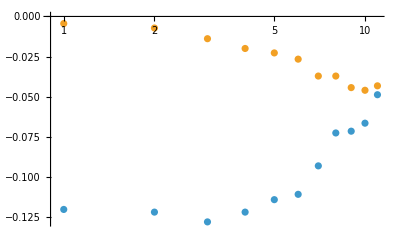

```mathematica
ListPlot[{R21STARp,R21STARap},ScalingFunctions->{"Log",Automatic}]
```

#### R31 data

```mathematica
sqrts=Transpose[Import["./fac_cumulants/R21_p.csv"]][[1]];
R31STARp=Transpose[Import["./fac_cumulants/R31_p_central.csv"]][[2]];
R31STARpstatup=Transpose[Import["./fac_cumulants/R31_p_statup.csv"]][[2]];
R31STARpsysup=Transpose[Import["./fac_cumulants/R31_p_sysup.csv"]][[2]];
R31pstaterr=R31STARpstatup-R31STARp;
R31psyserr=R31STARpsysup-R31STARp;
R31pdata=Transpose[{sqrts,Table[Around[R31STARp[[i]],R31pstaterr[[i]]],{i,1,Length[sqrts]}]}];
```

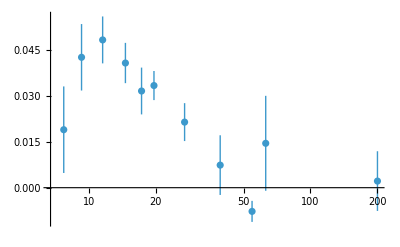

```mathematica
ListPlot[R31pdata,ScalingFunctions->{"Log",Automatic}]
```

#### R41 data

```mathematica
sqrts=Transpose[Import["./fac_cumulants/R21_p.csv"]][[1]];
R41STARp=Transpose[Import["./fac_cumulants/R41_p_central.csv"]][[2]];
R41STARpstatup=Transpose[Import["./fac_cumulants/R41_p_statup.csv"]][[2]];
R41STARpsysup=Transpose[Import["./fac_cumulants/R41_p_sysup.csv"]][[2]];
R41pstaterr=R41STARpstatup-R41STARp;
R41psyserr=R41STARpsysup-R41STARp;
R41pdata=Transpose[{sqrts,Table[Around[R41STARp[[i]],R41pstaterr[[i]]],{i,1,Length[sqrts]}]}];
```

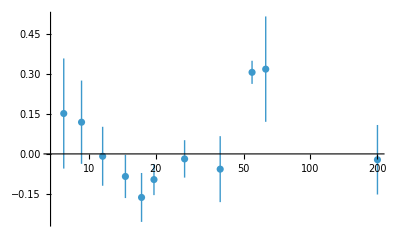

```mathematica
ListPlot[R41pdata,ScalingFunctions->{"Log",Automatic}]
```

### FXT data

```mathematica
STARfxtk21p={{3.0144508325499273,0.21880775245225795},{3.212862308631103,0.1361465194522105},{3.51004524114765,0.09328294555276487},{3.916406586875247,0.07488153343126555}};
STARfxtk31p={{3.003440402365993,-0.4687804878048784},{3.2025343490186224,-0.32390243902439025},{3.4980145862519096,-0.2248780487804876},{3.900400340942645,-0.12585365853658487}};
STARfxtk41p={{2.999999999999999,Around[-0.811024,0.0905512]},{3.200046493989738,Around[-0.353018,0.0695538]},{3.5007536670740844,Around[-0.128609,0.165354]},{3.900225889455326,Around[-0.541995,0.220472]}};
```

## Factorial cumulants fRG

```mathematica
fc1I=chi1STARI;
fc2I=chi2STARI-chi1STARI;
fc3I=chi3STARI-3chi2STARI+2chi1STARI;
fc4I=chi4STARI-6chi3STARI+11chi2STARI-6chi1STARI;

fc1II=chi1STARII;
fc2II=chi2STARII-chi1STARII;
fc3II=chi3STARII-3chi2STARII+2chi1STARII;
fc4II=chi4STARII-6chi3STARII+11chi2STARII-6chi1STARII;

fc1An=chi1An;
fc2An=chi2An-chi1An;
fc3An=chi3An-3chi2An+2chi1An;
fc4An=chi4An-6chi3An+11chi2An-6chi1An;
```

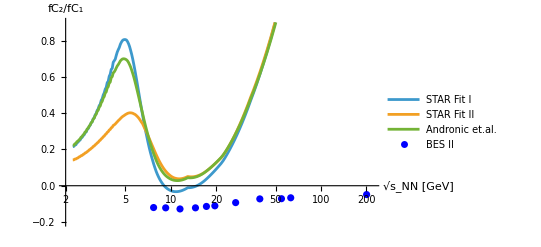

```mathematica
R21plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc2I/fc1I}],Transpose[{sqrtsfRG,fc2II/fc1II}],Transpose[{sqrtsfRG,fc2An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,220},{-0.2,0.9}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[Transpose[{sqrts,R21STARp}],ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],AxesLabel->{"√s_NN [GeV]","fC_2/fC_1"}]
```

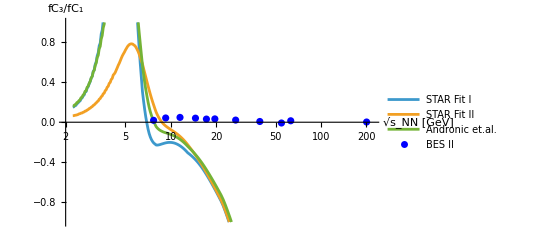

```mathematica
R31plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc3I/fc1I}],Transpose[{sqrtsfRG,fc3II/fc1II}],Transpose[{sqrtsfRG,fc3An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,220},{-1,1}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[R31pdata,ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],AxesLabel->{"√s_NN [GeV]","fC_3/fC_1"}]
```

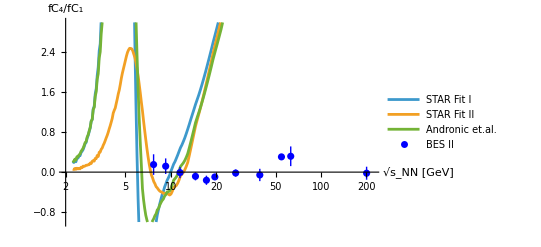

```mathematica
R41plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc4I/fc1I}],Transpose[{sqrtsfRG,fc4II/fc1II}],Transpose[{sqrtsfRG,fc4An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,220},{-1,3}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[R41pdata,ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],AxesLabel->{"√s_NN [GeV]","fC_4/fC_1"}]
```

```mathematica
Export["./R21plot.pdf",R21plot];
Export["./R31plot.pdf",R31plot];
Export["./R41plot.pdf",R41plot];
```

## Compare BES-I and BES-II

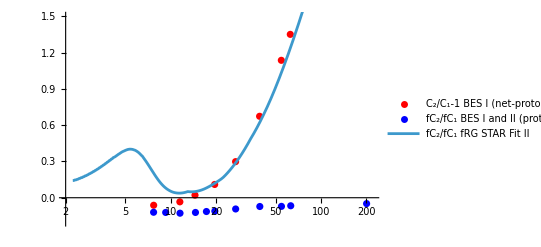

```mathematica
R21compare=Show[ListPlot[{Transpose[{sqrtr21,R21BESIdata-1}],Transpose[{sqrts,R21STARp}]},ScalingFunctions->{"Log",Automatic},PlotStyle->{Red,Blue},PlotLegends->{"C_2/C_1-1 BES I (net-proton)","fC_2/fC_1 BES I and II (proton)"},PlotRange->{{2,220},{-0.2,1.5}}],ListLinePlot[Transpose[{sqrtsfRG,fc2II/fc1II}],PlotRange->All,ScalingFunctions->{"Log"},PlotLegends->{"fC_2/fC_1 fRG STAR Fit II"}]]
```

```mathematica
Export["./BESR21compare.png",R21compare]
```

./BESR21compare.png

## SAM correction Ripples μ_(B,CEP)=650 MeV

```mathematica
Clear[alpha]
(*alpha[sqrts1_]:=0.33*(1-sqrts1/11.9)HeavisideTheta[1-sqrts1/11.9];*)
alpha[sqrts1_]:=0.33*(1-sqrts1/11.9)HeavisideTheta[1-sqrts1/11.9];
```

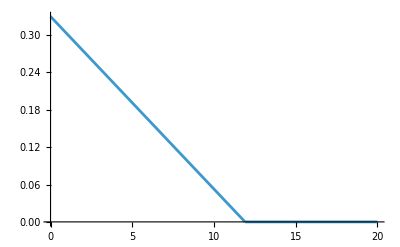

```mathematica
Plot[alpha[x],{x,0,20}]
```

```mathematica
SAMc1I=Table[chi1STARI[[i]] alpha[sqrtsfrg[[i]]],{i,1,Length[sqrtsfrg]}];
SAMc2I=Table[chi2STARI[[i]] alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc3I=Table[alpha[sqrtsfrg[[i]]]chi3STARI[[i]] (1-2alpha[sqrtsfrg[[i]]])(1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc4I=Table[alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])(chi4STARI[[i]]-3alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])*(chi3STARI[[i]]^2+chi2STARI[[i]]chi4STARI[[i]])/chi2STARI[[i]]),{i,1,Length[sqrtsfrg]}];
fc1I=SAMc1I;
fc2I=SAMc2I-SAMc1I;
fc3I=SAMc3I-3SAMc2I+2SAMc1I;
fc4I=SAMc4I-6SAMc3I+11SAMc2I-6SAMc1I;

SAMc1II=Table[chi1STARII[[i]] alpha[sqrtsfrg[[i]]],{i,1,Length[sqrtsfrg]}];
SAMc2II=Table[chi2STARII[[i]] alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc3II=Table[alpha[sqrtsfrg[[i]]]chi3STARII[[i]] (1-2alpha[sqrtsfrg[[i]]])(1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc4II=Table[alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])(chi4STARII[[i]]-3alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])*(chi3STARII[[i]]^2+chi2STARII[[i]]chi4STARII[[i]])/chi2STARII[[i]]),{i,1,Length[sqrtsfrg]}];
fc1II=SAMc1II;
fc2II=SAMc2II-SAMc1II;
fc3II=SAMc3II-3SAMc2II+2SAMc1II;
fc4II=SAMc4II-6SAMc3II+11SAMc2II-6SAMc1II;

SAMc1An=Table[chi1An[[i]] alpha[sqrtsfrg[[i]]],{i,1,Length[sqrtsfrg]}];
SAMc2An=Table[chi2An[[i]] alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc3An=Table[alpha[sqrtsfrg[[i]]]chi3An[[i]] (1-2alpha[sqrtsfrg[[i]]])(1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc4An=Table[alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])(chi4An[[i]]-3alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])*(chi3An[[i]]^2+chi2An[[i]]chi4An[[i]])/chi2An[[i]]),{i,1,Length[sqrtsfrg]}];
fc1An=SAMc1An;
fc2An=SAMc2An-SAMc1An;
fc3An=SAMc3An-3SAMc2An+2SAMc1An;
fc4An=SAMc4An-6SAMc3An+11SAMc2An-6SAMc1An;
```

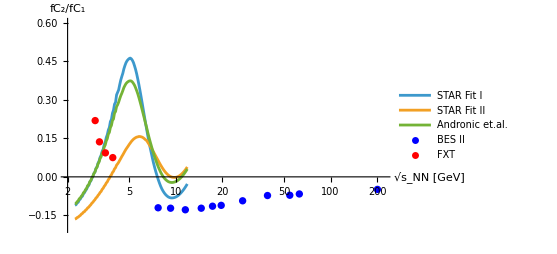

```mathematica
R21plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc2I/fc1I}],Transpose[{sqrtsfRG,fc2II/fc1II}],Transpose[{sqrtsfRG,fc2An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,220},{-0.2,0.6}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[Transpose[{sqrts,R21STARp}],ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],ListPlot[STARfxtk21p,ScalingFunctions->{"Log",Automatic},PlotStyle->Red,PlotLegends->{"FXT"}],AxesLabel->{"√s_NN [GeV]","fC_2/fC_1"}]//Quiet
```

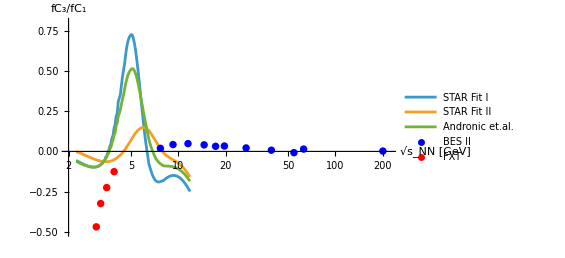

```mathematica
R31plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc3I/fc1I}],Transpose[{sqrtsfRG,fc3II/fc1II}],Transpose[{sqrtsfRG,fc3An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,220},{-0.5,0.8}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[R31pdata,ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],ListPlot[STARfxtk31p,ScalingFunctions->{"Log",Automatic},PlotStyle->Red,PlotLegends->{"FXT"}],AxesLabel->{"√s_NN [GeV]","fC_3/fC_1"}]//Quiet
```

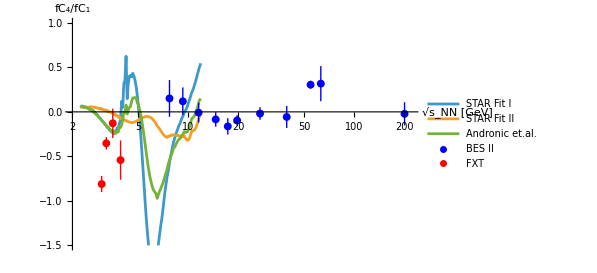

```mathematica
R41plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc4I/fc1I}],Transpose[{sqrtsfRG,fc4II/fc1II}],Transpose[{sqrtsfRG,fc4An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,220},{-1.5,1}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[R41pdata,ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],ListPlot[STARfxtk41p,ScalingFunctions->{"Log",Automatic},PlotStyle->Red,PlotLegends->{"FXT"}],AxesLabel->{"√s_NN [GeV]","fC_4/fC_1"}]//Quiet
```

## SAM correction Ruizhe

```mathematica
Clear[alpha]
alpha[sqrts1_]:=-3.720453139227731 +318.4673461884527/sqrts1^3-218.61397982042922/sqrts1^2+50.028910334509725/sqrts1;
```

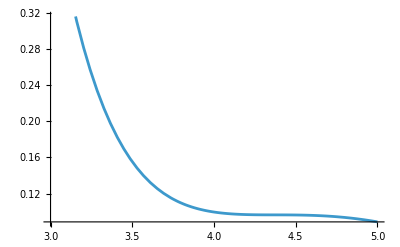

```mathematica
Plot[alpha[x],{x,3,5}]
```

```mathematica
SAMc1I=Table[chi1STARI[[i]] alpha[sqrtsfrg[[i]]],{i,1,Length[sqrtsfrg]}];
SAMc2I=Table[chi2STARI[[i]] alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc3I=Table[alpha[sqrtsfrg[[i]]]chi3STARI[[i]] (1-2alpha[sqrtsfrg[[i]]])(1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc4I=Table[alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])(chi4STARI[[i]]-3alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])*(chi3STARI[[i]]^2+chi2STARI[[i]]chi4STARI[[i]])/chi2STARI[[i]]),{i,1,Length[sqrtsfrg]}];
fc1I=SAMc1I;
fc2I=SAMc2I-SAMc1I;
fc3I=SAMc3I-3SAMc2I+2SAMc1I;
fc4I=SAMc4I-6SAMc3I+11SAMc2I-6SAMc1I;

SAMc1II=Table[chi1STARII[[i]] alpha[sqrtsfrg[[i]]],{i,1,Length[sqrtsfrg]}];
SAMc2II=Table[chi2STARII[[i]] alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc3II=Table[alpha[sqrtsfrg[[i]]]chi3STARII[[i]] (1-2alpha[sqrtsfrg[[i]]])(1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc4II=Table[alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])(chi4STARII[[i]]-3alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])*(chi3STARII[[i]]^2+chi2STARII[[i]]chi4STARII[[i]])/chi2STARII[[i]]),{i,1,Length[sqrtsfrg]}];
fc1II=SAMc1II;
fc2II=SAMc2II-SAMc1II;
fc3II=SAMc3II-3SAMc2II+2SAMc1II;
fc4II=SAMc4II-6SAMc3II+11SAMc2II-6SAMc1II;

SAMc1An=Table[chi1An[[i]] alpha[sqrtsfrg[[i]]],{i,1,Length[sqrtsfrg]}];
SAMc2An=Table[chi2An[[i]] alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc3An=Table[alpha[sqrtsfrg[[i]]]chi3An[[i]] (1-2alpha[sqrtsfrg[[i]]])(1-alpha[sqrtsfrg[[i]]]),{i,1,Length[sqrtsfrg]}];
SAMc4An=Table[alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])(chi4An[[i]]-3alpha[sqrtsfrg[[i]]](1-alpha[sqrtsfrg[[i]]])*(chi3An[[i]]^2+chi2An[[i]]chi4An[[i]])/chi2An[[i]]),{i,1,Length[sqrtsfrg]}];
fc1An=SAMc1An;
fc2An=SAMc2An-SAMc1An;
fc3An=SAMc3An-3SAMc2An+2SAMc1An;
fc4An=SAMc4An-6SAMc3An+11SAMc2An-6SAMc1An;
```

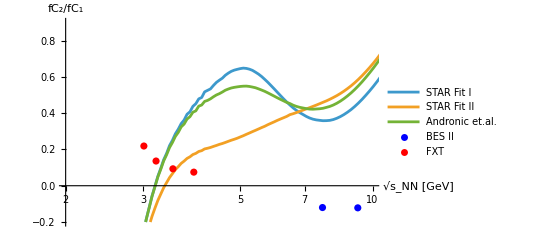

```mathematica
R21plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc2I/fc1I}],Transpose[{sqrtsfRG,fc2II/fc1II}],Transpose[{sqrtsfRG,fc2An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,10},{-0.2,0.9}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[Transpose[{sqrts,R21STARp}],ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],ListPlot[STARfxtk21p,ScalingFunctions->{"Log",Automatic},PlotStyle->Red,PlotLegends->{"FXT"}],AxesLabel->{"√s_NN [GeV]","fC_2/fC_1"}]
```

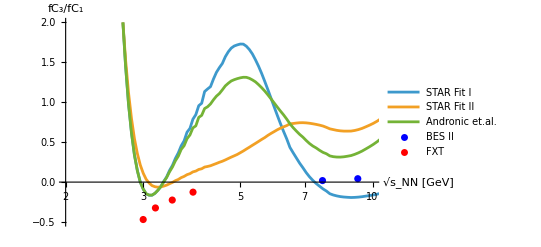

```mathematica
R31plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc3I/fc1I}],Transpose[{sqrtsfRG,fc3II/fc1II}],Transpose[{sqrtsfRG,fc3An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,10},{-0.5,2}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[R31pdata,ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],ListPlot[STARfxtk31p,ScalingFunctions->{"Log",Automatic},PlotStyle->Red,PlotLegends->{"FXT"}],AxesLabel->{"√s_NN [GeV]","fC_3/fC_1"}]
```

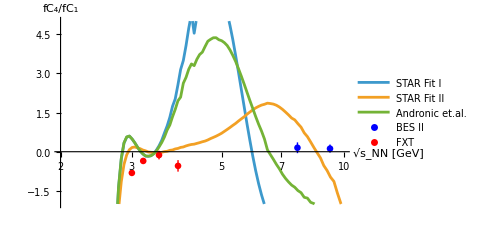

```mathematica
R41plot=Show[ListLinePlot[{Transpose[{sqrtsfRG,fc4I/fc1I}],Transpose[{sqrtsfRG,fc4II/fc1II}],Transpose[{sqrtsfRG,fc4An/fc1An}]},ScalingFunctions->{"Log",Automatic},PlotRange->{{2,10},{-2,5}},PlotLegends->{"STAR Fit I","STAR Fit II","Andronic et.al."}],ListPlot[R41pdata,ScalingFunctions->{"Log",Automatic},PlotStyle->Blue,PlotLegends->{"BES II"}],ListPlot[STARfxtk41p,ScalingFunctions->{"Log",Automatic},PlotStyle->Red,PlotLegends->{"FXT"}],AxesLabel->{"√s_NN [GeV]","fC_4/fC_1"}]
```

## alpha between C1p and C1pbar

```mathematica
sqrts2=Transpose[Import["./BESI/proton_C1.csv"]][[1]];
C1p=Transpose[Import["./BESI/proton_C1.csv"]][[2]];
C1pb=Transpose[Import["./BESI/antiproton_C1.csv"]][[2]];
C2p=Transpose[Import["./BESI/proton_C2.csv"]][[2]];
C2pb=Transpose[Import["./BESI/antiproton_C2.csv"]][[2]];
alpha=C1pb/C1p;
C1tot=(1+alpha)C1p;
C1net=(1-alpha)C1p;
r21pfc=C2p/C1p-1;
```

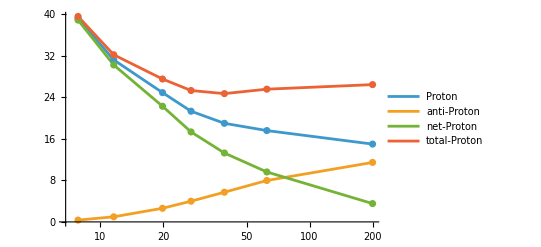

```mathematica
Show[ListLinePlot[{Transpose[{sqrts2,C1p}],Transpose[{sqrts2,C1pb}],Transpose[{sqrts2,C1net}],Transpose[{sqrts2,C1tot}]},ScalingFunctions->{"Log",Automatic},PlotLegends->{"Proton","anti-Proton","net-Proton","total-Proton"}],ListPlot[{Transpose[{sqrts2,C1p}],Transpose[{sqrts2,C1pb}],Transpose[{sqrts2,C1net}],Transpose[{sqrts2,C1tot}]},ScalingFunctions->{"Log",Automatic}]]
```

```mathematica
sqrtr21={7.7,11.5,19.6,27,39,62.4,200};
R21BESI={0.937634,0.965991,1.10972,1.29862,1.67391,2.35186,6.6121};
```

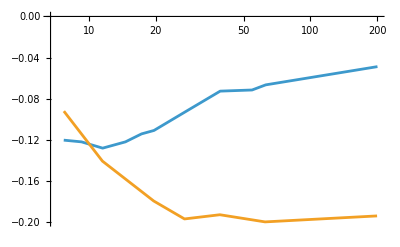

```mathematica
ListLinePlot[{Transpose[{sqrts,R21STARp}],Transpose[{sqrtr21,r21pfc}]},ScalingFunctions->{"Log",Automatic},PlotRange->All]
```

```mathematica
R21fc=R21BESI-C1tot/C1net;
```

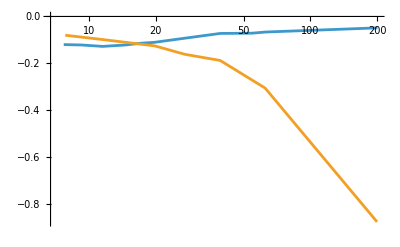

```mathematica
ListLinePlot[{Transpose[{sqrts,R21STARp}],Transpose[{sqrts2,R21fc}]},ScalingFunctions->{"Log",Automatic},PlotRange->All]
```